## Task 3 _ 1

## Variant 3

```mathematica
NN = 3.0; CC = 2.7; BB = 0.1;
```

```mathematica
X = {0.53, 1.1, 1.4, 2.57, CC, 2.8, 3.7, 4.5}
```

{0.53,1.1,1.4,2.57,2.7,2.8,3.7,4.5}

```mathematica
Y = {BB, 0.33, 1.0, 1.7,  0.0, 3.4, 4.1, NN}
```

{0.1,0.33,1.,1.7,0.,3.4,4.1,3.}

```mathematica
lists = {}
```

{}

```mathematica
For[i=1, i≤Length[X], i++,
AppendTo[lists, {X⟦i⟧,Y⟦i⟧}]
]
```

```mathematica
lists
```

{{0.53,0.1},{1.1,0.33},{1.4,1.},{2.57,1.7},{2.7,0.},{2.8,3.4},{3.7,4.1},{4.5,3.}}

## Кусочно-постоянная интерполяция :

```mathematica
lin = Interpolation[lists,InterpolationOrder->1]
```

InterpolatingFunction[{{0.53, 4.5}}, <>]

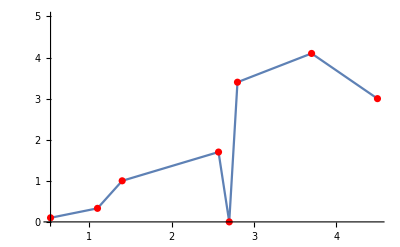

```mathematica
Show[Plot[lin[x],{x,0.53,4.5},PlotRange->{0,5}],ListPlot[lists, PlotStyle->Red]]
```

## Сплайн интерполяция :

```mathematica
lists
```

{{0.53,0.1},{1.1,0.33},{1.4,1.},{2.57,1.7},{2.7,0.},{2.8,3.4},{3.7,4.1},{4.5,3.}}

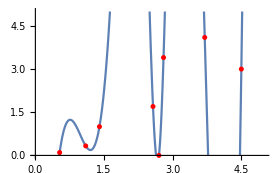

```mathematica
sp = Interpolation[lists, InterpolationOrder->3,Method->"Spline"];
Show[Plot[sp[x],{x,0,5},PlotRange->{0,5}],ListPlot[lists, PlotStyle->Red]]
```

## Кубическая интерполяция:

```mathematica
n = Length[X]
```

8

```mathematica
s[j_]:=(p = j;If[j>3, p=j-4]; p)
```

```mathematica
ni[t_]:=∑_(i = 2)^(n-3) If[t-X⟦i+1⟧>0, 1 ,0]
```

```mathematica
iFunc[t_, i_, j_]:=((t-X⟦i+s[j+1]⟧)*(t-X⟦i+s[j+2]⟧)*(t-X⟦i+s[j+3]⟧))/((X⟦i+s[j]⟧-X⟦i+s[j+1]⟧)*(X⟦i+s[j]⟧-X⟦i+s[j+2]⟧)*(X⟦i+s[j]⟧-X⟦i+s[j+3]⟧))
```

```mathematica
P[t_, i_]:=Y⟦i⟧*iFunc[t, i, 0]+Y⟦i+1⟧*iFunc[t, i, 1]+Y⟦i+2⟧*iFunc[t, i, 2]+Y⟦i+3⟧*iFunc[t, i, 3]
```

```mathematica
PL[t_]:= P[t, ni[t]+1]
```

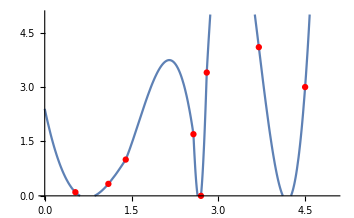

```mathematica
Show[Plot[PL[x],{x,0,5},PlotRange->{0,5}],ListPlot[lists, PlotStyle->Red]]
```

## Производная кусочно-постоянной интерполяции:

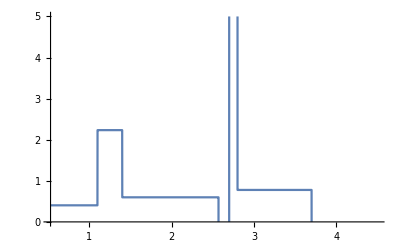

```mathematica
Plot[lin'[x],{x,0.53,4.5},PlotRange->{0,5}]
```

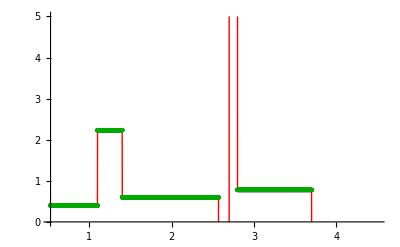

```mathematica
Show[Plot[lin'[x],{x,0.53,4.5},PlotRange->{0,5}, PlotStyle->{Red,Thick}],ListPlot[lin'[Range[First[X], Last[X], 0.0001]],DataRange->{First[X], Last[X]},PlotStyle-> {Darker[Green],PointSize[Medium]},PlotRange->{0,5}]]
```

## Производная сплайн интерполяции:

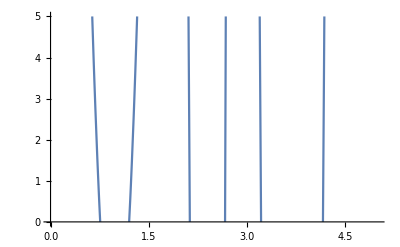

```mathematica
Plot[sp'[x],{x,0,5},PlotRange->{0,5}]
```

```mathematica
Show[Plot[sp'[x],{x,0,5},PlotRange->{0,5}, PlotStyle->Red],ListPlot[sp'[Range[First[X], Last[X], 0.00001]],DataRange->{First[X], Last[X]},PlotStyle-> {Darker[Green],PointSize[Small]},PlotRange->{0,5}]]
```

-Graphics-

## Производная кубической интерполяции :

Part::pkspec1: The expression 1+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

Part::pkspec1: The expression 2+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

Part::pkspec1: The expression 3+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

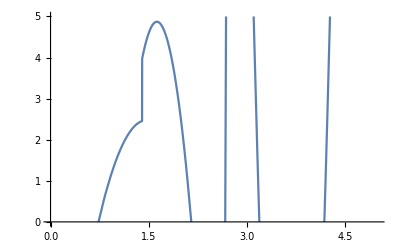

```mathematica
Plot[PL'[x],{x,0,5},PlotRange->{0,5}]
```

Part::pkspec1: The expression 1+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

Part::pkspec1: The expression 2+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

Part::pkspec1: The expression 3+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

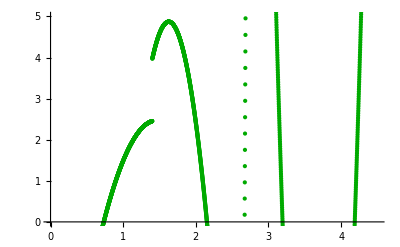

```mathematica
ListPlot[PL'[#]&/@Range[First[X], Last[X], 0.001],DataRange->{First[X], Last[X]},PlotStyle-> {Darker[Green],PointSize[Small]},PlotRange->{0,5}]
```

Part::pkspec1: The expression 1+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

Part::pkspec1: The expression 2+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

Part::pkspec1: The expression 3+If[-2.8+#1>0,1,0]+If[-2.7+#1>0,1,0]+If[-2.57+#1>0,1,0]+If[-1.4+#1>0,1,0] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

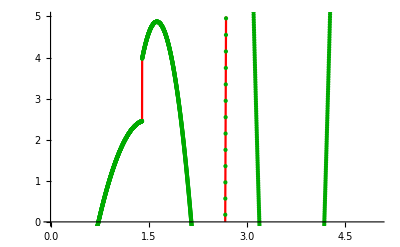

```mathematica
Show[Plot[PL'[x],{x,0,5},PlotRange->{0,5}, PlotStyle->Red],ListPlot[PL'[#]&/@Range[First[X], Last[X], 0.001],DataRange->{First[X], Last[X]},PlotStyle-> {Darker[Green],PointSize[Small]},PlotRange->{0,5}]]
```

```mathematica
(* 3. Записать в общем виде формулу для вычисление значения X для X3<X<X4,в случае кусочно-постоянной,кусочно-кубической и сплайн–интерполяции.
 4. Укажите на графике точки в которых нарушается дифференцируемость функций. *)
```

## Task 3 _ 2

```mathematica
line = Fit[lists, {1,x},x]
```

-0.502931+0.914687 x

```mathematica
parabola=Fit[lists, {1,x, x^2},x]
```

-0.568461+0.98638 x-0.014536 x^2

```mathematica
cubic = Fit[lists, {1,x,x^2,x^3},x]
```

1.23968-2.39897 x+1.54981 x^2-0.203414 x^3

```mathematica
sin = Fit[lists,{1,Sin[x]},x]
```

2.15818-1.66906 Sin[x]

```mathematica
TrigToExp[sin]
```

2.15818-(0.+0.834528 ⅈ) ⅇ^(-ⅈ x)+(0.+0.834528 ⅈ) ⅇ^(ⅈ x)

```mathematica
exp = Fit[lists,{1, Exp[x]},x]
```

0.941639+0.0332051 ⅇ^x

```mathematica
ln =Fit[lists,{Log[x]},x]
```

2.05543 Log[x]

```mathematica
deg = Fit[lists,{1,x^x},x]
```

1.41048+0.002248 x^x

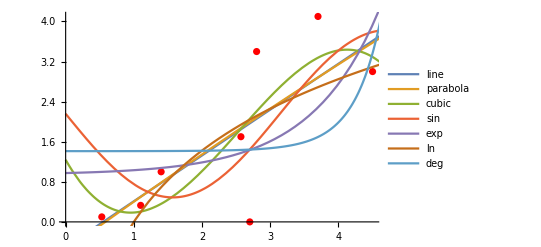

```mathematica
Show[ListPlot[lists, PlotStyle->Red], Plot[{line, parabola, cubic,sin,exp, ln, deg}, {x, 0, 5},PlotLegends->"Expressions"]]
```

```mathematica
deviation[param_]:= (
Sqrt[∑_(i=1)^n ((param/.x ->X⟦i⟧)-Y⟦i⟧)^2/n]
)
```

```mathematica
parabS = deviation[parabola]
```

0.977288

```mathematica
cubicS = deviation[cubic]
```

0.931301

```mathematica
expS = deviation[exp]
```

1.18867

```mathematica
lnS = deviation[ln]
```

1.11575

```mathematica
sinS = deviation[sin]
```

1.06644

```mathematica
degS =  deviation[deg]
```

1.36641

```mathematica
max[param_]:= (
Max[Table[Abs[(param/.x ->X⟦i⟧)-Y⟦i⟧],{i,1,n}]]
)
```

```mathematica
maxParab =max[parabola]
```

1.9888

```mathematica
maxCubic = max[cubic]
```

2.05675

```mathematica
maxExp =  max[exp]
```

1.91231

```mathematica
maxSin = max[sin]
```

1.80093

```mathematica
maxLn = max[ln]
```

2.04156

```mathematica
maxDeg = max[deg]
```

2.40498